# Harper — PS 3 — 2025-01-24

## Sections 9-11

### Section 9

```mathematica
Manipulate[Range[n],{n,1,100,1}]
```

```mathematica
Manipulate[ListPlot[Range[n]],{n,5,50,1}]
```

```mathematica
Manipulate[Column[Table[x,n]],{n,1,10,1}]
```

```mathematica
Manipulate[Graphics[Style[Disk[],Hue[n]]],{n,0,1}]
```

```mathematica
Manipulate[Graphics[Style[Disk[],RGBColor[r,g,b]]],{r,0,1},{g,0,1},{b,0,1}]
```

```mathematica
Manipulate[IntegerDigits[n],{n,1000,9999,1}]
```

```mathematica
Manipulate[Table[Hue[h],{h,0,1,n}],{n,0.2,0.02}]
```

```mathematica
Manipulate[Table[Graphics[Style[RegularPolygon[6],Hue[h]]],n],{h,0,1},{n,1,10,1}]
```

```mathematica
Manipulate[Graphics[Style[RegularPolygon[s],{c}]],{s,5,20,1},{c,{Red,Yellow,Blue}}]
```

```mathematica
Manipulate[PieChart[Table[1,n]],{n,1,10,1}]
```

```mathematica
Manipulate[BarChart[IntegerDigits[n]],{n,100,999,1}]
```

```mathematica
Manipulate[RandomColor[n],{n,1,50,1}]
```

```mathematica
Manipulate[b^e,{b,1,25,1},{e,1,10,1}]
```

```mathematica
Manipulate[NumberLinePlot[Range[b]^e],{b,1,10,1},{e,0,5,1}]
```

```mathematica
Manipulate[Graphics3D[Style[Sphere[],RGBColor[r,1-r,0]]],{r,0,1}]
```

```mathematica
Manipulate[ListPlot[Range[100]^p],{p,-1,1}]
```

```mathematica
Manipulate[Style[1000,s],{s,5,100,1}]
```

```mathematica
Manipulate[BarChart[{a,b,c,d}],{a,0,10},{b,0,10},{c,0,10},{d,0,10}]
```

### Section 10

```mathematica
ColorNegate[EdgeDetect[-Graphics-]]
```

-Graphics-

```mathematica
Manipulate[Blur[-Graphics-,n],{n,0,20}]
```

```mathematica
Table[EdgeDetect[Blur[-Graphics-,n]],{n,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageCollage[{Blur[-Graphics-],EdgeDetect[-Graphics-],Binarize[-Graphics-]}]
```

-Graphics-

```mathematica
ImageAdd[-Graphics-,Binarize[-Graphics-]]
```

-Graphics-

```mathematica
Table[EdgeDetect[Blur[-Graphics-,n]],{n,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EdgeDetect[Graphics3D[Sphere[]]]
```

-Graphics-

```mathematica
Manipulate[Blur[Graphics[Style[RegularPolygon[5],Purple]],n],{n,0,20}]
```

```mathematica
ImageCollage[Table[Graphics[Style[Disk[],RandomColor[]]],9]]
```

-Graphics-

```mathematica
ImageCollage[Table[Graphics3D[Style[Sphere[],Hue[n]]],{n,0,1,0.2}]]
```

-Graphics-

```mathematica
Table[Blur[Graphics[Disk[]],n],{n,0,30,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageAdd[-Graphics-,Graphics[Disk[]]]
```

-Graphics-

```mathematica
ImageAdd[-Graphics-,Graphics[Style[RegularPolygon[8],Red]]]
```

-Graphics-

```mathematica
ImageAdd[-Graphics-,ColorNegate[EdgeDetect[-Graphics-]]]
```

-Graphics-

### Section 11 - 11.1-11.15

```mathematica
StringJoin["Hello","Hello"]
```

HelloHello

```mathematica
ToUpperCase[StringJoin[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

```mathematica
StringJoin[Reverse[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

```mathematica
StringJoin[Table["AGCT",100]]
```

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

```mathematica
StringTake[StringJoin[Alphabet[]],6]
```

abcdef

```mathematica
Column[Table[StringTake["this is about strings.",n],{n,22}]]
```

t
th
thi
this
this 
this i
this is
this is 
this is a
this is ab
this is abo
this is abou
this is about
this is about 
this is about s
this is about st
this is about str
this is about stri
this is about strin
this is about string
this is about strings
this is about strings.

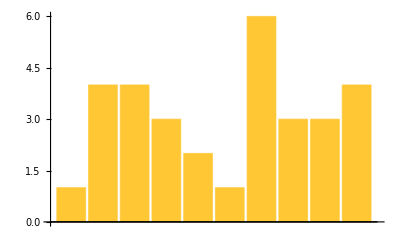

```mathematica
BarChart[StringLength[TextWords["A long time ago, in a galaxy far, far away."]]]
```

```mathematica
StringLength[WikipediaData["computers"]]
```

60266

```mathematica
First[TextSentences[WikipediaData["strings"]]]
```

String or strings may refer to:

```mathematica
StringJoin[StringTake[TextSentences[WikipediaData["computers"]],1]]
```

AMTTACCESEMTTTCTPP=ITTDBTTTT==DTLTTTSITIIDMTTAAATTTIASIBIAITITIITSI=CCAHTFTTTAEBNH=ITax()2{,THI=DHTTTTAB==CBTDETTITIRTZTT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAATBAIL=TJFCJTHATHTTWITT=TTDTKIHKNNHPNIMTGFTTWISTITS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIETWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCICW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITTSTTITMWITC=PUTTS=MF=ATHHIT=PALTP=ETHOBSA=CTITTITCITA"=AWA=TMH=TQCVSLTTT=ACARPE=AT=====M

```mathematica
Max[StringLength[WordList[]]]
```

23

```mathematica
Count[StringTake[WordList[],1],"q"]
```

194

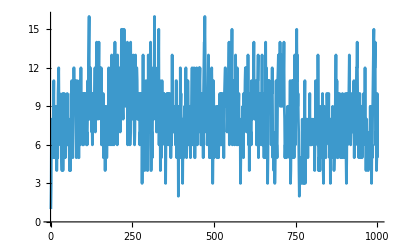

```mathematica
ListLinePlot[Take[StringLength[WordList[]],1000]]
```

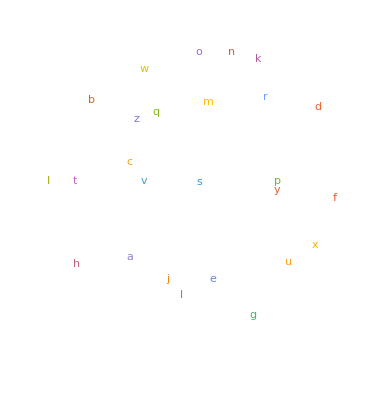

```mathematica
WordCloud[StringTake[WordList[],1]]
```